# Mass Functions

This is a collection of routines to compute mass functions. 
Based on M. White, ApJS 2002

```mathematica
Needs["Cosmology`MassFunction`"];
```

## Multiplicity functions

We start by defining the multiplicity function :
	 \nu f(\nu) d\nu = \frac{M}{2 \bar{\rho}} \frac{dn}{dM} dM
where 
	\nu = \delta_c / \sigma(M)
Reorganizing the above somewhat, we get 
	 = dn/dM = (2 \bar{\rho} / M)  \nu^2 f(\nu) (d \ln(\nu)/ dM) =  -  (2 \bar{\rho} / M)  \nu^2 f(\nu) (d \sigma(M)/ dM)

Below, we define a number of these multiplicity functions - Press-Schechter and Sheth-Tormen as well as code to compute sigma(M) and its derivatives to get the mass function. Note that
we define the multiplicity function to by \nu f(\nu)

## Bias

Within the peak background split, the bias may be calculated by differentiation ln (dn/dM) with respect to delta_c. This is more conveniently done by using 
	d \nu/ d \delta_c =  \nu / \delta_c
Note that the way we have written the above expressions, only \nu^2 f(\nu) depends on \delta_c

Note that the 1+ term above is to convert to Eulerian bias.

### Normalization

The normalization of the multiplicity function νf(ν) is normalized such that ∫νf(ν) dν = 1/2. We explicitly test this below (the normalizations above were adjusted so that this is true).

```mathematica
Integrate[PressSchechter[v],{v,0, Infinity}]
```

1/2

Note that the ShethTormen normalization is a floating point number....

```mathematica
Integrate[ShethTormen[v], {v, 0, Infinity}]
```

0.5

## Testing

```mathematica
bPS[x_]:=bias[PressSchechter, x] /. {deltac -> 1.686};
```

```mathematica
bST[x_]:=bias[ShethTormen, x] /. {deltac -> 1.686};
```

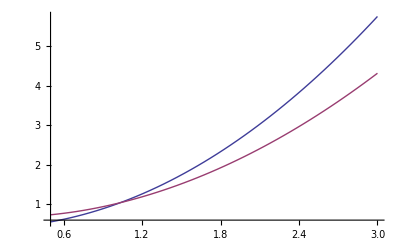

```mathematica
Plot[{bPS[x], bST[x]}, {x, 0.5, 3.0}]
```